```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lyliana/Wolfram Mathematica/FIsExp/Espectroscopia

```mathematica
ExpandFileName["/home/lyliana/Wolfram Mathematica/FIsExp/Espectroscopia"]
```

/home/lyliana/Wolfram Mathematica/FIsExp/Espectroscopia

```mathematica
(*Dados do espectro do mercurio, utilizado para a calibração
Coluna1 = pixel; Coluna2 = intensidade*)
especmercurio = Import["calibraçãomercurio.dat"];
(*Dados do espectro do hidrôgenio
Coluna1 = pixel; Coluna2 = intensidade*)
espechidrogenio = Import["espectrohidrogênio2.dat"];
(*Dados da linearização do mercurio para obter a calibração dos pixel pelo comprimento de onda
Coluna1 = pixel; Coluna2 = comprimento*)
dadosmercurio = Import["mercuriopixelcomprimento.dat"];
(*Dados do hidrogênio para a linearização e a obtenção da constante de Rydberg
Coluna1 = pico; Coluna2 = intensidade; Coluna3 = comprimento [angnstron]; Coluna4 = inc.comprimento; Coluna5 = 1/lambda; Coluna6 = inc. 1/lambda; Coluna7 = n*)
dadoshidrogenio = Import["hidrogenio.dat"];
```

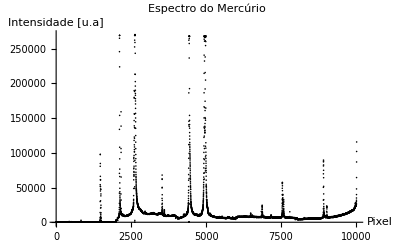

```mathematica
(*gráfico do espectro do Hg*)
espectromercurio = ListPlot[especmercurio,PlotRange->Full, PlotLabel->"Espectro do Mercúrio", AxesLabel->{"Pixel","Intensidade [u.a]"}, PlotStyle->ColorData[3]]
```

```mathematica
(*Ajuste linear da calibração do mercúrio*)
mercurio[t_]:= (A*t) + B 
ajustemercurio = NonlinearModelFit[dadosmercurio,mercurio[t], {{A, 0.595},{B,2043}},t];
ajustemercurio["BestFitParameters"]
ajustemercurio["ParameterErrors"]
ajustemercurio["AdjustedRSquared"]
```

{A→0.609339,B→2763.14}

{0.00616374,21.0963}

0.999985

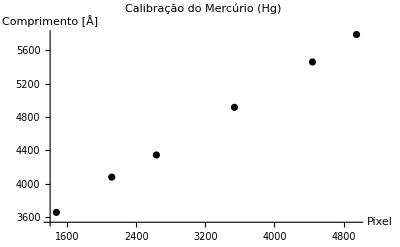

```mathematica
(*A tabela de dados das linhas do Hg obtidas,com uma coluna para a posição da linha em pixel e outra para o comprimento de onda  tabelado*)
calibracaomercurio = ListPlot[dadosmercurio, PlotLabel->"Calibração do Mercúrio (Hg)", AxesLabel->{"Pixel","Comprimento [Å]"}, PlotStyle->ColorData[3]]
```

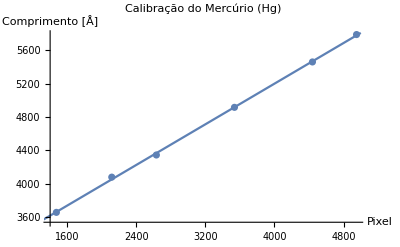

```mathematica
Show[{ListPlot[dadosmercurio],Plot[mercurio[x]/.ajustemercurio["BestFitParameters"],{x,0 ,5000}]},PlotLabel-> "Calibração do Mercúrio (Hg)", AxesLabel->{"Pixel","Comprimento [Å]"}]
```

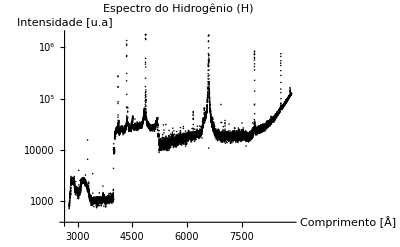

```mathematica
(*gráfico do espectro do H*)
espectrohidrogenio = ListLogPlot[espechidrogenio, PlotRange->Full, PlotLabel->"Espectro do Hidrogênio (H)", AxesLabel->{"Comprimento [Å]","Intensidade [u.a]"}, PlotStyle->ColorData[3]]
```

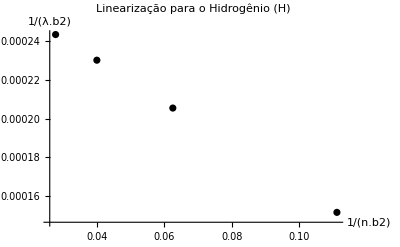

```mathematica
(*A tabela de dados das linhas do H obtidas,com a posição das linhas em pixel,o comprimento de onda calculado e o estado inicial (n) da transição*)
linearhidrogenio = ListPlot[dadoshidrogenio, PlotLabel->"Linearização para o Hidrogênio (H)", AxesLabel->{" 1/(n.b2)","1/(λ.b2)"}, PlotStyle->ColorData[3]]
```

```mathematica
(*Ajuste linear da calibração do hidrogenio*)
hidrogenio[t_]:= A*(1/2^2 - t)
ajustehidrogenio = NonlinearModelFit[dadoshidrogenio,hidrogenio[t], {{A, 10^-3}},t];
ajustehidrogenio["BestFitParameters"]
ajustehidrogenio["ParameterErrors"]
ajustehidrogenio["AdjustedRSquared"]
```

{A→0.0010956}

{9.3094×10^-7}

0.999997

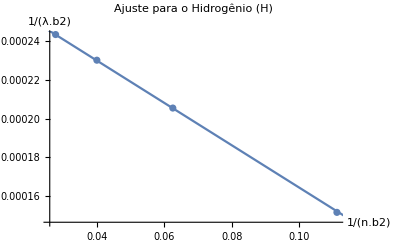

```mathematica
Show[{ListPlot[dadoshidrogenio],Plot[hidrogenio[x]/.ajustehidrogenio["BestFitParameters"],{x,0 ,6.1}]}, PlotLabel->"Ajuste para o Hidrogênio (H)", AxesLabel->{" 1/(n.b2)","1/(λ.b2)"}, PlotStyle->ColorData[3]]
```

```mathematica
{A->0.0010956018915391122}
{9.309401478742028*^-7}
```

{A→0.0010956}

{9.3094×10^-7}

R_H = (1.0956e7± 2e3) 1/m

```mathematica
(*Terei que refazer a calibração dos pixels*)
(*Dados da segunda coleta do espectro do mercurio, utilizado para a calibração
Coluna1 = pixel; Coluna2 = intensidade*)
recalibraçãoespecmercurio = Import["recalibraçãomercurio.dat"];
```

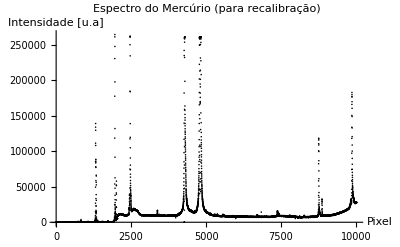

```mathematica
(*gráfico do espectro do Hg*)
espectromercurio = ListPlot[recalibraçãoespecmercurio,PlotRange->Full, PlotLabel->"Espectro do Mercúrio (para recalibração)", AxesLabel->{"Pixel","Intensidade [u.a]"}, PlotStyle->ColorData[3]]
```

```mathematica
(*Dados da linearização do mercurio para obter a calibração dos pixel pelo comprimento de onda
Coluna1 = pixel; Coluna2 = comprimento*)
dadosrecalibraçãomercurio = Import["recalibraçãomercuriopixelcomprimento.dat"];
```

```mathematica
(*Ajuste linear da  recalibração do mercúrio*)
remercurio[t_]:= (A*t) + B 
reajustemercurio = NonlinearModelFit[dadosrecalibraçãomercurio,remercurio[t], {{A, 0.595},{B,2043}},t];
reajustemercurio["BestFitParameters"]
reajustemercurio["ParameterErrors"]
reajustemercurio["AdjustedRSquared"]
```

{A→0.605857,B→2874.31}

{0.00563499,18.4374}

0.999987

```mathematica
{A,B}/.{A->0.6058574000808759,B->2874.3117693886425}
```

{0.605857,2874.31}

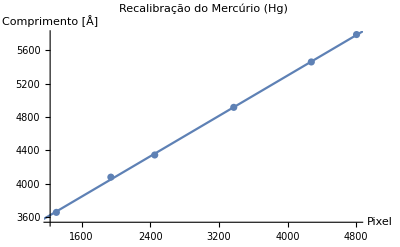

```mathematica
(*A tabela de dados das linhas do Hg obtidas,com uma coluna para a posição da linha em pixel e outra para o comprimento de onda  tabelado*)
Show[{ListPlot[dadosrecalibraçãomercurio],Plot[remercurio[x]/.reajustemercurio["BestFitParameters"],{x,0 ,5000}]},PlotLabel-> "Recalibração do Mercúrio (Hg)", AxesLabel->{"Pixel","Comprimento [Å]"}]
```

```mathematica
(*Dados do espectro do hidrôgenio
Coluna1 = comprimento; Coluna2 = intensidade*)
especsodio = Import["especsodio.dat"];
```

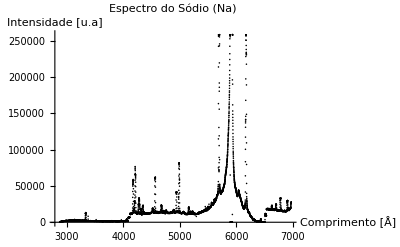

```mathematica
(*gráfico do espectro do Na*)
espectrohidrogenio = ListPlot[especsodio, PlotRange->Full, PlotLabel->"Espectro do Sódio (Na)", AxesLabel->{"Comprimento [Å]","Intensidade [u.a]"}, PlotStyle->ColorData[3]]
```

{R→1.23157×10^7,p→0.78586,d→-0.0379162,s→1.28992}

{772723.,0.0582936,0.0660582,0.0485596}

0.99993

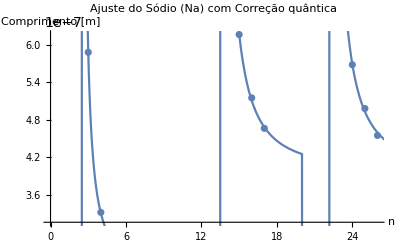

```mathematica
(*Ajuste não linear série difusa*)
dadosajuste = Import["espectroscopia.dat"];
quanticoajuste[n_]:=1/R*(((1/(1/(3- s)^2 - 1/(n - p)^2)) *If[n<10, 1, 0]) +((1/(1/(3- p)^2 - 1/(n - 10 -s)^2)) *If[10<n<20, 1, 0]) +((1/(1/(3- p)^2 - 1/(n -20- d)^2))*If[n>20, 1, 0]))
ajustequantico = NonlinearModelFit[dadosajuste,quanticoajuste[n],{{R,1.1*10^7},{p,0.87},{d,0.01},{s,1.37}},n];
ajustequantico["BestFitParameters"]
ajustequantico["ParameterErrors"]
ajustequantico["AdjustedRSquared"]
Show[{ListPlot[dadosajuste],Plot[quanticoajuste[x]/.ajustequantico["BestFitParameters"],{x,0 ,28}]},PlotLabel-> "Ajuste do Sódio (Na) com Correção quântica", AxesLabel->{"n","Comprimento [m]"}]
```

```mathematica
pontosD = Import["ajustesodioD.dat"];
pontosP = Import["ajustesodioP.dat"];
pontosN = Import["ajustesodioN.dat"];
SerieD = ListPlot[pontosD, Joined->True,InterpolationOrder->None,Mesh->Full,PlotLabels->{"Série Difusa"},PlotStyle-> {Green}];
SerieP = ListPlot[pontosP, Joined->True,InterpolationOrder->None,Mesh->Full,PlotLabels->{"Série Principal"},PlotStyle-> {Yellow}];
SerieN= ListPlot[pontosN, Joined->True,InterpolationOrder->None,Mesh->Full,PlotLabels->{"Série Nítida"},PlotStyle-> {Red}];
Show[{SerieD,SerieP,SerieN}, PlotRange-> {{3,8},{3*10^-7,6.1*10^-7}}, Axes -> False, Frame -> True, PlotLabel-> "Série principal, nítida e difusa do Sódio (Na)", FrameLabel->{"n","Comprimento [m]"}]
```

-Graphics-